```mathematica
Clear["Global`*"]
```

```mathematica
dNdt=r N(1-N/K)-c N^2 P/(1+c h N^2)
```

-(c N^2 P)/(1+c h N^2)+N (1-N/K) r

```mathematica
parms={r->1, K->10,P->1,h->0.5, c->2};
subparms={r->1, K->10,P->1,h->0.5};
```

```mathematica
equil=Simplify[Solve[dNdt==0,N]];
equil/.parms
```

{{N→0},{N→0.683375+2.96059×10^-16 ⅈ},{N→7.31662-1.4803×10^-16 ⅈ},{N→2.-2.96059×10^-16 ⅈ}}

```mathematica
LineCols={{Orange,Thickness[0.01]},{Red,Thickness[0.01]},{Blue,Thickness[0.01]},{Green, Thickness[0.01]}};
```

```mathematica
equil2=equil[[All,1,2]]/.subparms;
```

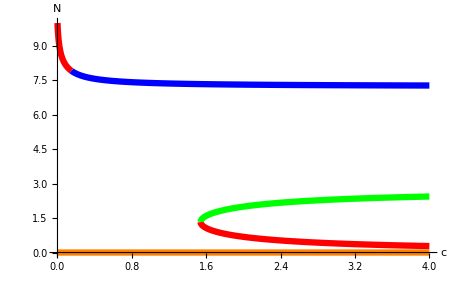

```mathematica
Plot[equil2,{c,0,4},AxesLabel->{c,N},PlotStyle->LineCols]
```

```mathematica
DdNdt=D[dNdt,N]
```

(2 c^2 h N^3 P)/((1+c h N^2)^2)-(2 c N P)/(1+c h N^2)-(N r)/K+(1-N/K) r

```mathematica
DdNdt2=DdNdt/.equil/.subparms;
```

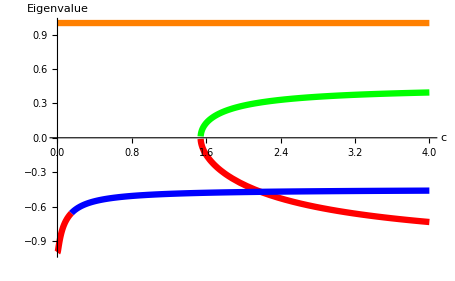

```mathematica
Plot[DdNdt2,{c,0,4},PlotStyle->LineCols,AxesLabel->{c,Eigenvalue}]
```

```mathematica
(* Return time = -1/lambda *)
RT=-1/D[dNdt,N]
```

-1/((2 c^2 h N^3 P)/((1+c h N^2)^2)-(2 c N P)/(1+c h N^2)-(N r)/K+(1-N/K) r)

```mathematica
RT2=RT/.equil/.subparms;
```

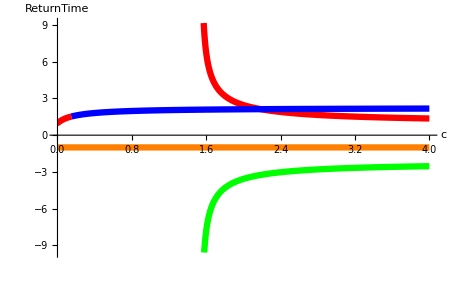

```mathematica
Plot[RT2,{c,0,4},PlotStyle->LineCols,AxesLabel->{c,ReturnTime}]
```

```mathematica
pN=-Integrate[dNdt,N]
```

(N P)/h-(N^2 r)/2+(N^3 r)/(3 K)-(P ArcTan[√c √h N])/(√c h^(3/2))

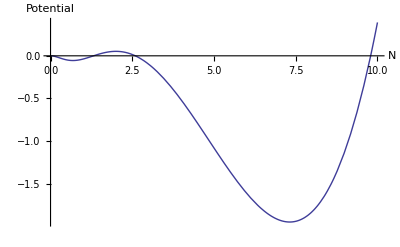

```mathematica
Plot[pN/.parms,{N,0,10},AxesLabel->{N,Potential}]
```

```mathematica
Plot3D[pN/.subparms,{c,2,2.1},{N,0,10},AxesLabel->{c,N,Potential}]
```

Plot3D::invisop: {} must be a valid 2D coordinate.

-Graphics3D-

```mathematica
(* With handling time (1/max feeding rate), like in half-saturation parameterized model *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
dNdt=r N(1-N/K)-c N^2 P/(1+c h N^2)
```

-(c N^2 P)/(1+c h N^2)+N (1-N/K) r

```mathematica
parms={r->1, K->10,P->1, c->2,h->0.5};
subparms={r->1, K->10,P->1,c->2};
```

```mathematica
equil=Simplify[Solve[dNdt==0,N]];
equil/.parms
```

{{N→0},{N→0.683375+2.96059×10^-16 ⅈ},{N→7.31662-1.4803×10^-16 ⅈ},{N→2.-2.96059×10^-16 ⅈ}}

```mathematica
LineCols={{Orange,Thickness[0.01]},{Red,Thickness[0.01]},{Blue,Thickness[0.01]},{Green, Thickness[0.01]}};
```

```mathematica
equil2=equil[[All,1,2]]/.subparms;
```

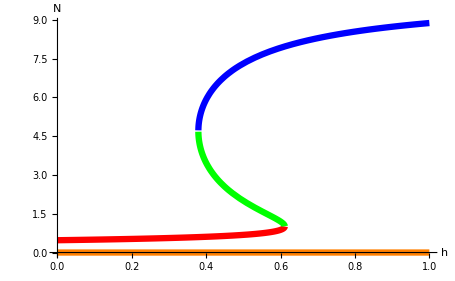

```mathematica
Plot[equil2,{h,0,1},AxesLabel->{h,N},PlotStyle->LineCols]
```

```mathematica
DdNdt=D[dNdt,N]
```

(2 c^2 h N^3 P)/((1+c h N^2)^2)-(2 c N P)/(1+c h N^2)-(N r)/K+(1-N/K) r

```mathematica
DdNdt2=DdNdt/.equil/.subparms;
```

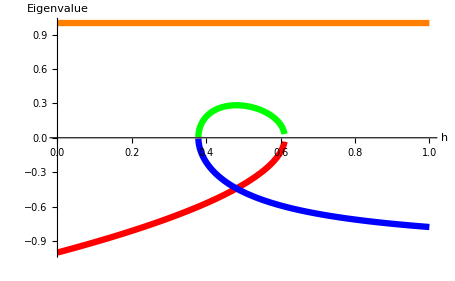

```mathematica
Plot[DdNdt2,{h,0,1},PlotStyle->LineCols,AxesLabel->{h,Eigenvalue}]
```

```mathematica
(* Return time = -1/lambda *)
RT=-1/D[dNdt,N]
```

-1/((2 c^2 h N^3 P)/((1+c h N^2)^2)-(2 c N P)/(1+c h N^2)-(N r)/K+(1-N/K) r)

```mathematica
RT2=RT/.equil/.subparms;
```

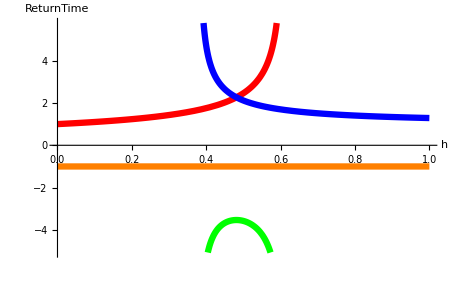

```mathematica
Plot[RT2,{h,0,1},PlotStyle->LineCols,AxesLabel->{h,ReturnTime}]
```

```mathematica
pN=-Integrate[dNdt,N]
```

(N P)/h-(N^2 r)/2+(N^3 r)/(3 K)-(P ArcTan[√c √h N])/(√c h^(3/2))

```mathematica
Plot[pN/.parms,{N,0,10},AxesLabel->{N,Potential}]
```

-Graphics-

```mathematica
Plot3D[pN/.subparms,{h,0,1},{N,0,10},AxesLabel->{h,N,Potential}]
```

Plot3D::invisop: {} must be a valid 2D coordinate.

-Graphics3D-